```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Defino la función que devuelve los valores de u y v para tiempo posterior para dados parámetros mu,nu,dx,dt y los valores de u y v anteriores*)
Turing[u_,v_,dx_,dt_,mu_,nu_]:=Module[{J,unew,vnew,pos,g1,g2},
(*Defino las funciones g1 y g2 dadas en las ecuaciones diferenciales*)
g1[a_,b_]:=1/32(-7 a^2 - 50 a b + 57);
g2[a_,b_]:=1/32(7 a^2 + 50 a b - 2 b - 55);
J = Length[u]+1;
(*Defino la función que garantiza la periodicidad*)
pos[k_]:=If[Mod[k,J-1]≠0,Mod[k,J-1],J-1];
(*Creo vectores auxiliares unew y vnew*)
unew = ConstantArray[0,Length[u]];vnew=ConstantArray[0,Length[u]];
(*Uso (3.9) para determinar uj^(n+1) donde j es el índice en la grilla espacial*)
Do[
unew⟦pos[j]⟧ = u⟦pos[j]⟧+ dt/dx^2 mu(u⟦pos[j+1]⟧- 2 u⟦pos[j]⟧ +u⟦pos[j-1]⟧) + dt g1[u⟦pos[j]⟧, v⟦pos[j]⟧];
vnew⟦pos[j]⟧ = v⟦pos[j]⟧ + dt/dx^2 nu(v⟦pos[j+1]⟧ - 2 v⟦pos[j]⟧ + v⟦pos[j-1]⟧) + dt g2[u⟦pos[j]⟧, v⟦pos[j]⟧]; 
,{j,1,Length[u]}];
{unew,vnew}];
```

```mathematica
(*Test de función pos[k] dado un vector u de tamaño 6*)
j = 1;
J = 6+1; (*6 es el tamaño de la grilla*)
If[Mod[j,J-1]≠0,Mod[j,J-1],L-1]
```

```mathematica
(*Test de Turing*)
(*
dx = 0.1;
dt = 0.01; (*tamaño de la unidad en la red periódica espacial. dx = dt = dz ya que la grilla es uniforme*)
L = 1.; (*tamaño de la red periódica espacial*)
tmax = 2;

D1 = 0.01; mu =D1; nu =D1/2; (*tengo que llamarlo D1 porque D is protected*)
A = 0.1; B = 0.1;

u = RandomReal[{-A,A},L/dx]+1;v = RandomReal[{-B,B},L/dx]+1;
Print[u,v]
{u,v}=Turing[u,v,dx,dt,mu,nu];
Print[u,v]
Datos = ConstantArray[0,{IntegerPart[tmax/dt + 1], IntegerPart[L/dx + 1] ,2}];
*)
```

```mathematica
(*Test de gráficos: *)
(*
Datos[[1 ]] = Transpose[{u,v}];
ListPlot[{Datos[[1, ;; , 1]],Datos[[1, ;; , 2]]}, Joined ->True, Mesh->All]
k = 2;
Datos[[k]] = Transpose[Turing[Datos[[k-1, ;; , 1]] ,Datos[[k-1, ;; , 2]] ,dx,dt,mu,nu]]
ListPlot[{Datos[[k, ;; , 1]],Datos[[k, ;; , 2]]}, Joined->True, Mesh->All]
k = 3;
Datos[[k]] = Transpose[Turing[Datos[[k-1, ;; , 1]] ,Datos[[k-1, ;; , 2]] ,dx,dt,mu,nu]]
ListPlot[{Datos[[k, ;; , 1]],Datos[[k, ;; , 2]]}, Joined->True, Mesh->All]
*)
```

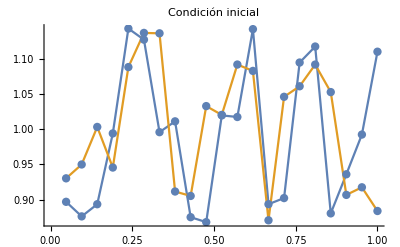

```mathematica
(*Tamaños de la unidad en la red periódica espacial y temporal: *)
dx = 0.01;
dt = 0.001;
(*Tamaños de la red periódica espacial y temporal*)
L = 1.; (*longitud total de la malla*)
tmax = 10.;

(*Parámetros de la Ecuación diferencial*)
D1 = 0.01; mu =D1; nu =D1/2; (*tengo que llamarlo D1 porque D is protected*)
A = 0.15; B = 0.15; (*Amplitud de u y v alrededor del equilibrio, respectivamente. A,B<0.15 recordando que son perturbaciones*)
(*Inicializo u y v con números random: condiciones iniciales al azar (uniformes) para ambas variables, con un parámetro (A para u, B para v) que controle la amplitud alrededor del valor de equilibrio homogéneo u* = 1, v* = 1;*)
u = RandomReal[{-A,A},L/dx + 1]+1;v = RandomReal[{-B,B},L/dx + 1]+1;
(*Creo la matriz en la que guardaré todos los datos*)
Datos = ConstantArray[0,{IntegerPart[tmax/dt + 1], IntegerPart[L/dx + 1] ,2}];
(*Inicializo la matriz con los valores random*)
Datos[[1]] = Transpose[{u,v}];
(*Creo la lista de la red espacial*)
malla = N[Range[Length[u]]/Length[u]];
(*Grafico la condición inicial*)
ListPlot[{Transpose[{malla, Datos[[1,All,1]]}],Transpose[{malla, Datos[[1,All,2]]}]}, PlotLabel->"Condición inicial", Mesh->All, Joined->True]
```

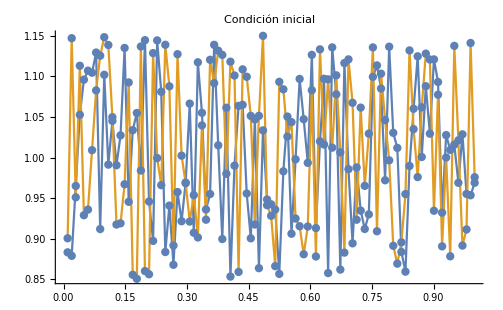

```mathematica
(**)
Do[
Datos[[k]] = Transpose[Turing[Datos[[k-1, ;; , 1]] ,Datos[[k-1, ;; , 2]] ,dx,dt,mu,nu]];
,{k,2,tmax/dt}];
(*Test de gráfico*)
(*
k = 20;
ListPlot[{Transpose[{malla, Datos[[k,All,1]]}], Transpose[{malla, Datos[[k,All,2]]}]}, Joined->True, Mesh->All]
*)
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

```mathematica
pasos = 100; (*cada cuantas iteraciones grafica*)
Manipulate[
u = Datos[[k, All , 1]];
v = Datos[[k, All , 2]];
ListPlot[{Transpose[{malla,u}],Transpose[{malla,v}]},Joined->False, Mesh->All, PlotRange->{{0,1},{-2*A+1,2*A+1}}, PlotLabel->"dx = " <> ToString[dx] <> ", dt = " <> ToString[dt] <> ", D = " <> ToString[D1] <> " - Tiempo: " <> ToString[k*dt] <> " s"]
,{k,1,IntegerPart[tmax/dt],pasos}]

(*Si hago la malla uniforme con dx = dt el programa se muere con dz = 0.01*)
(*No llego a curvas lindas en el equilibrio. No se parecen a senos y cosenos, sino a combinación de ellos*)
(*A tiempos largos la animación sigue cambiando*)
```

Part::partw: Part 63901 of … does not exist.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,1⟧} cannot be transposed.

Part::partw: Part 63901 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,2⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 63901 of {{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»} does not exist.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,2⟧} cannot be transposed.

Part::partw: Part 63901 of {{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.0909091,0.181818,0.272727,0.363636,0.454545,0.545455,0.636364,0.727273,0.818182,0.909091,1.},{{{0.889722,0.866557},{1.02539,1.02807},{0.862282,0.994205},{1.14242,0.959946},{0.850005,1.04325},{1.13608,1.0937},{0.994729,1.04899},{0.974552,1.10621},{1.06263,1.13656},{1.0489,0.922144},{0.880906,1.04533}},«49»,«19951»}⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,2⟧} cannot be transposed.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,2⟧} cannot be transposed.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,2⟧} cannot be transposed.

Part::partw: Part 63901 of {{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},{1.1434,1.08856},{1.12764,1.13721},{0.995875,1.13664},{1.01129,0.91138},{0.874817,0.905069},«4»,{0.893345,0.870384},{0.902028,1.04622},{1.09503,1.06124},{1.11783,1.09214},{0.880244,1.05295},{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},{«1»},«47»,{«1»},«39951»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428571,0.47619,0.52381,0.571429,0.619048,0.666667,0.714286,0.761905,0.809524,0.857143,0.904762,0.952381,1.},{{{0.896707,0.930144},{0.875945,0.949875},{0.893281,1.00331},{0.994115,0.945515},«14»,{0.935915,0.906561},{0.992474,0.917381},{1.11045,0.883635}},«49»,«39951»}⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification Datos⟦63901,All,1⟧ is longer than depth of object.

Part::partd: Part specification Datos⟦63901,All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0}},Datos⟦63901,All,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0}},Datos⟦63901,All,2⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.},{2.,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0},{0,0,0,0,0,0,1.,0}},Datos⟦63901,All,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{0,1},{1-2 A,1+2 A}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

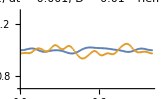
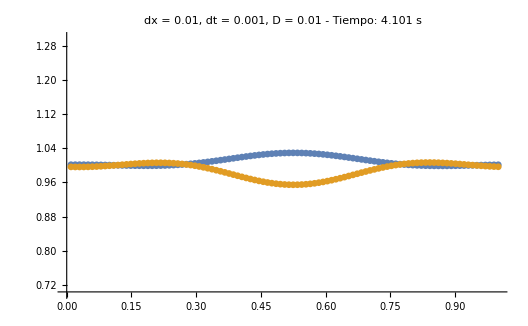
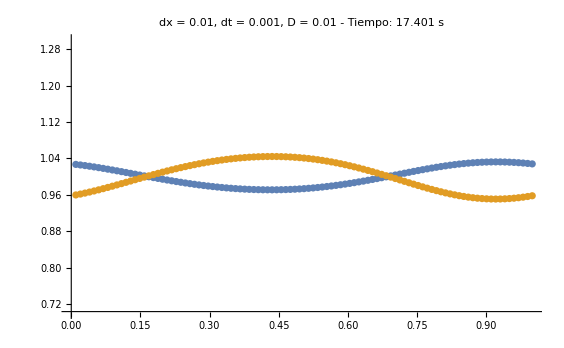
```mathematica
(*Evolución temporal*)
-Graphics--Graphics--Graphics-
```

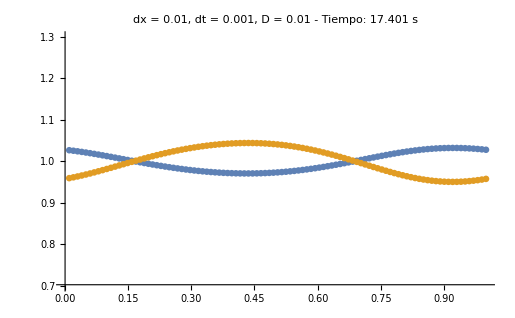
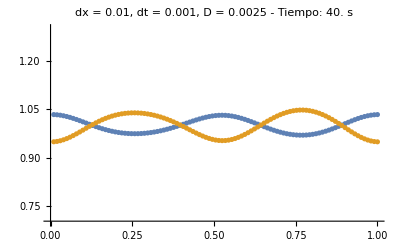
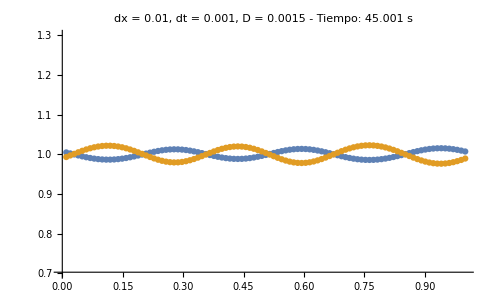
Gráficos obtenidos

D parámetro de la EDP, K número de onda determinado gráficamente, tmin tiempo mínimo necesario para llegar al estado estacionario. Esta última definición es muy vaga dado que el estado estacionario se determina visualmente.
D = 0.01	k = 2 pi	tmin = 17.4 s
D = 0.0025	k = 4 pi	tmin = 40 s
D = 0.0015	k = 5 pi	tmin = 45 s 
D = 0.001	k = 10 pi	tmin = 50.2 s 
D = 0.00075	k = 10 pi	tmin = 102 s (más tiempo ?)
D = 0.0005	k = 	tmin = 


-Graphics--Graphics--Graphics-